```mathematica
Needs["PiCbench`"]
```

## 1- Magnitudes

```mathematica
MagnitudeList[]
```

Variable | Value | Definition
$dx | 1 | $dx:=1
$nx | 1024 | $nx:=1024
$qp | 0.0004 | $qp:=0.0004
$mp | 0.0004 | $mp:=0.0004
$np | 3000 | $np:=3000
$ionMass | 1836.15 | $ionMass:=1836.15
$dt | 1 | $dt:=1
$a | 1 | $a:=1
$b | 1 | $b:=1
$c | 1 | $c:=1
$charSpeed | 0.5 | $charSpeed:=0.5
$charSpeedIons | 0.0116685 | $charSpeedIons:=($charSpeed)/(√($ionMass))
$lx | 1024 | $lx:=$dx $nx
$wp | 0.0342327 | $wp:=√(($np ($qp)^2 $a)/($lx $mp))
$debyeLength | 14.6059 | $debyeLength:=($charSpeed)/($wp)

```mathematica
$dx::usage
```

Length of cell size in the x dimenssion

```mathematica
PrintConditions[]
```

Small cell condition - ($dx<<$lx) - 1 << 1024

Small time-step condition - ($dt<<$wp^-1) - 1 << 29.2119

Big world condition - ($debyeLength<<$lx) - 14.6059 << 1024

{Null,Null,Null}

```mathematica
$charSpeed=10;
```

```mathematica
PrintConditions[]
```

Small cell condition - ($dx<<$lx) - 1 << 1024

Small time-step condition - ($dt<<$wp^-1) - 1 << 29.2119

Big world condition - ($debyeLength<<$lx) - 292.119 << 1024

{Null,Null,Null}

```mathematica
$charSpeed=0.5;
```

## 2- Initialization

```mathematica
?UniformParticles1D
```

Generates a uniform particle distribution in [0, lx] x [-vmax,vmax].

```mathematica
UniformParticles1D[lx->$lx,vmax->$charSpeed*2,np->10]
```

{{652.366,0.0239234},{737.695,0.270707},{636.625,-0.206022},{329.248,-0.00270019},{185.435,0.72195},{842.347,-0.356465},{285.68,-0.0238122},{103.367,0.431767},{183.06,-0.32818},{890.599,-0.534325}}

```mathematica
electrons=UniformParticles1D[vmax->$charSpeed*2];
```

```mathematica
ions=UniformParticles1D[vmax->$charSpeedIons*2];
```

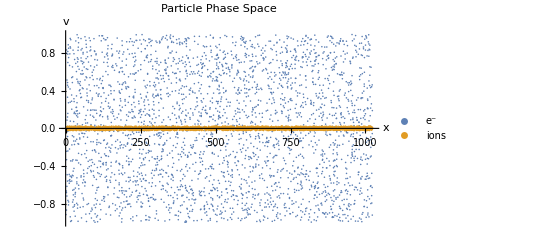

```mathematica
PhaseSpacePlot[{electrons,ions},PlotLegends->{"e^-","ions"}]
```

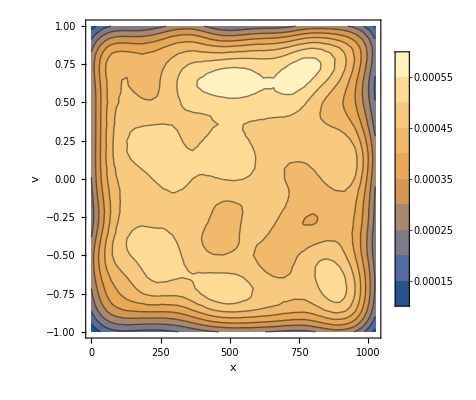

```mathematica
SmoothPhaseSpacePlot[electrons,PlotLegends->Automatic]
```

## 3- Particle to grid

```mathematica
?getRho1D
```

getRho1D[] returns a functions that calculates rho(particleList). Options include dx,nx,qc. Use with qc=1 to find number density.

A trick to see the code in a cleaned style:

```mathematica
Begin["PiCbench`Particle2Grid`Private`"];
Quiet[getRho1D[nx->"nx",dx->"dx",qp->"qp",Method->"First-order"],{Table::iterb}]
End[];
```

Function[{particles},Block[{rho,pos,x,i},rho=Table[0.,{1+nx}];For[i=1,i≤Length[particles],i++,x=particles⟦i,1⟧;pos=Floor[x];rho⟦pos+1⟧+=pos+1-x;rho⟦pos+2⟧+=x-pos;];rho⟦1⟧+=rho⟦nx+1⟧;(Drop[rho,-1] qp)/dx]]

Use should be made by using a compiled function

```mathematica
getρ=FCompile[getRho1D[],{_Real},{2},CompilationTarget->"C",RuntimeOptions->"Speed"]
```

CompiledFunction[…]

Automatic benchmark of compilation:

```mathematica
TableForm[{BenchmarkFCompile[{getRho1D[],{_Real},{2}},{electrons},100],BenchmarkFCompile[{getRho1D[Method->"Zeroth-order"],{_Real},{2}},{electrons},100]},TableHeadings->{{"1st","0th"},{"None","WVM","C","CSpeed"}}]
```

| None | WVM | C | CSpeed
1st | 0.0222915 | 0.00048165 | 0.00016819 | 0.00005398
0th | 0.012499 | 0.00022123 | 0.0001258 | 0.00006339

```mathematica
ρElectron=getρ[electrons];
```

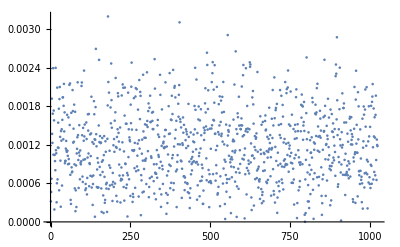

```mathematica
ListPlot[ρElectron]
```